# Projektrapport 1 - Algebra

(Rapportskalet använder sig av ett stylesheet tillverkat av Göran Andersson)

Evan Saboo, Emil Nordin & Perttu Jääskeläinen

## 1. Introduktion: problemformulering

Inom matematikkursen har vi fått i uppgift att lösa tre olika matematiska problem med hjälp av Mathematica och dess programmeringsspråk. Målet med den första projektet är att öva matematisk modellering, kunna ställa upp och utföra enklare matrisoperationer i  Mathematica och kunna lösa linjära ekvationssystem.

### 1.1 Uppgift 1 - Polynomanpassning

I Första uppgiften skulle man hitta fjärdegradspolynomet f(t) = a+ b t + c t^2+d t^3+e t^4  som går igenom punkterna (1,1), (2,-1), (3,-59), (-1,5) och (-2,-29).

I första deluppgiften skulle man ställa upp en matris och finnas lösningen för hand för att hitta funtkionen
Den andra uppgiften gick det ut på att använda Mathematica för att hitta fjärdegradspolynomet, och  kontrollera lösningen genom återsubstitution samt plotta polynomet i en figur.

### 1.2 Uppgift 2 - Industriproduktion

Tre st företag sålde en del av sina produktioner till konsumenter och resten såldes till andra företag.

Den andra uppgiften gick ut på att man skulle ställa upp linjära ekvationssystem och lösa ut p1, p2 och p3 med hjälp av mathematica som visar hur stor produktionen på vardera av de tre företagen (F1, F2 och F3) måste vara för att tillgodose det totala produktionsbehovet. Bilden nedan illustrerar hur mycket produktion varje företag sålde till konsumenter och till andra företag.
-Graphics-

### 1.3 Uppgift 3 - Linjärtransformationer och grafik

Den sista uppgiften handlade om linjärtransformationer y=Ax , där x och y är vektorer och A en transformationsmatris.
Man skulle ta den första bokstaven i förnamnet på en i er grupp och låta 4-6 punkter (i 2D) representera bokstaven i x-y planet.
Sedan skulle man ta  fram transformationsmatrisen A för fyra olika operationer och repesentera dem i sin egen figur med hjälp av Mathematica.
De fyra operationer var:
1. Skalning till dubbla storleken.
2. Inversen , dvs y=-x. 
3. Rotation 90 grader kring y-axeln
4. Horisontell skuvning (valfritt hur stor men inte lika med noll !)

## 2 Genomförande och härledningar

### 2.1 Uppgift 1 - Polynomanpassning

#### a)

Deluppgiften kommer att presenteras i redovisningen med färdiga lösningar.

#### b)

Först använde vi datatypen ClearAll för att rensa alla globala variblar från dess värden, sedan tilldelade vi den generalla frjärdegradspolynomet till f(t) för att kunna förenkla funktionen med bestämda punkter . Efter att ha förenklat alla punkter med sin egen funktion tilldelade lösningarna till matrisen p.
För att lösa ut frjärdegradspolynomet med de angivna punkterna använde vi oss av datatypen RowReduce för att få den reducerade formen av matrisen p. Vi använde oss också av MatrixForm för att få ut lösningen på matrisform och för att det ska se snyggare ut.

```mathematica
ClearAll["`*"]
```

```mathematica
f[t_]:=a+ b*t +c*t^2+d*t^3+e*t^4
```

```mathematica
f[1]==1
```

a+b+c+d+e==1

```mathematica
f[2]==-1
```

a+2 b+4 c+8 d+16 e==-1

```mathematica
f[3]==-59
```

a+3 b+9 c+27 d+81 e==-59

```mathematica
f[-1]==5
```

a-b+c-d+e==5

```mathematica
f[-2]==-29
```

a-2 b+4 c-8 d+16 e==-29

```mathematica
Clear[f]
```

```mathematica
p:={ {1,1,1,1,1,1},{1,2,4,8,16,-1},{1,3,9,27,81,-59},{1,-1,1,-1,1,5}, {1,-2,4,-8,16,-29}}
```

```mathematica
RowReduce[p]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | -5
0 | 0 | 1 | 0 | 0 | 4
0 | 0 | 0 | 1 | 0 | 3
0 | 0 | 0 | 0 | 1 | -2)

Efter att ha reducerat matrisen var det dags att tilldela lösningar i frjärdegradspolynomet  f(t) = a+ b t + c t^2+d t^3+e t^4, där a = 1, b = -5, c = 4, d = 3 och e=-2.
Med hjälp av datatypen Solve kunde vi kontrollera om funktionen f(t) stämde med alla angivna punkter genom att tex sätta t = 3 i funktionen som ledde till att vi fick svaret y=-59, vilket stämde  med punkten (3,-59).

```mathematica
f[t_] = 1 -5t+4t^2 + 3t^3 -2t^4
```

1-5 t+4 t^2+3 t^3-2 t^4

```mathematica
Solve[f[1]==y1,y1]
```

{{y1→1}}

```mathematica
Solve[f[2]==y2,y2]
```

{{y2→-1}}

```mathematica
Solve[f[3]==y3,y3]
```

{{y3→-59}}

```mathematica
Solve[f[-1]==y4,y4]
```

{{y4→5}}

```mathematica
Solve[f[-2]==y5,y5]
```

{{y5→-29}}

Efter att ha hittat och kontrollerat funktion f(t) var det dags att plotta den med hjälp av datatypen Plot.

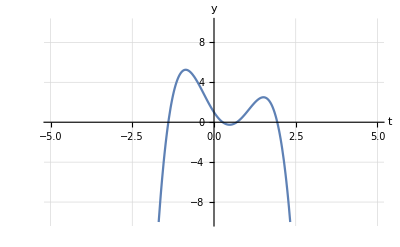

```mathematica
Plot[f[t], {t, -5, 5}, AxesLabel -> {t,y}, PlotRange ->{-10, 10}, LabelStyle->(FontSize->16), GridLines->Automatic]
```

### 2.2 Uppgift 2 - Industriproduktion

För att lösa den andra uppgiften började vi med att tilldela varje företag med sitt eget värde, vilket var antalet sålda produktioner till konsumenter. Därefter adderade vi andelarna företaget gav bort, dvs att företag 1 gav bort 0.2 av hela p2’s produktion och 0.3 av p3’s produktion. Sedan använde vi funktionen “Solve” i Mathematica för att programmet skulle räkna ut svaret åt oss, vilket resulterade i det svar vi har nedan.

```mathematica
ClearAll["`*"]
```

```mathematica
F1:= 320
F2:=90
F3:=150
```

```mathematica
Solve[{p1==F1+0.2p2+0.3p3,
p2==F2+0.4p3+0.1p1,
p3==F3+0.2p1+0.5p2},{p1,p2,p3}]
```

{{p1→500.,p2→300.,p3→400.}}

### 2.3 Uppgift 3 - Linjärtransformationer och grafik

#### a)

I den första deluppgiften skulle man ta fram tranformationmatrisen A  för att skala upp en grupp med 4-6 punkter till dubbel storlek, gruppen kallades för bostaven e. 
I Mathematica använde vi oss av ScalingTransformation för att skala up punkternas x-kordinat och y-kordinat till dubbel storleken, uppskalningen skedde med tranformationsmatrien A=(2 | 0 | 0
0 | 2 | 0
0 | 0 | 1).

```mathematica
ClearAll["`*"]
```

```mathematica
e:={{1,1},{4,3},{8,9},{16,5}}
```

```mathematica
eScal=ScalingTransform[{2,2}]
```

TransformationFunction[(2 | 0 | 0
0 | 2 | 0
0 | 0 | 1)]

```mathematica
eScaled=eScal[e]
```

{{2,2},{8,6},{16,18},{32,10}}

Efter skalningen plottade vi den vanliga e och den upppskalade e tillsammans med hjälp av funktionen “Plot” för att kunna jämföra båda med varandra.

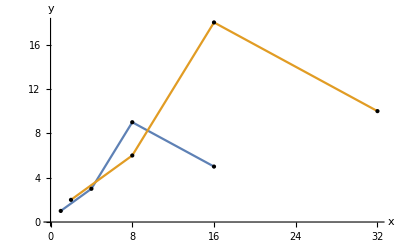

```mathematica
ListLinePlot[{e,eScaled},AxesLabel->{x,y},Epilog->{PointSize[Large],Point[e],Point[eScaled]}]
```

#### b)

Den andra deluppgiften gick ut på att använda invers tranformationmatris A på martisen e. Vi tog A=(-1 | 0 | 0
0 | 1 | 0
0 | 0 | 1) eftersom invers är y=-x för där bara x-kordinaten blir negativ i punkterna.
Med hjälp av Mathematica funtkionen “ReflectionTranform”  kunde vi få ut “spegel” matrisen e som vi plottade sen med den vanliga e.

```mathematica
eInv=ReflectionTransform[{1,0}]
```

TransformationFunction[(-1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)]

```mathematica
eInverse=eInv[e]
```

{{-1,1},{-4,3},{-8,9},{-16,5}}

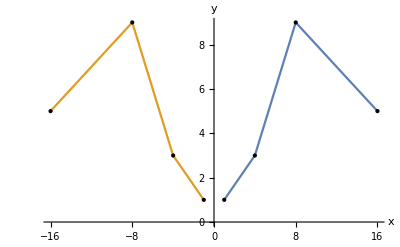

```mathematica
ListLinePlot[{e,eInverse},AxesLabel->{x,y},Epilog->{PointSize[Large],Point[e],Point[eInverse]}]
```

#### c)

“RotationTransform” var den rätta Mathematica funktionen för att rotera matrisen e i 90 grader runt y axeln, där tranformationsmatrisen blev A= (0 | -1 | 0
1 | 0 | 0
0 | 0 | 1). Som de förra uppgifterna plottade vi också den roterade e med de vanliga e för at kunna jämföra dem med varandra.

```mathematica
eRot= RotationTransform[Pi/2]
```

TransformationFunction[(0 | -1 | 0
1 | 0 | 0
0 | 0 | 1)]

```mathematica
eRotated=eRot[e]
```

{{-1,1},{-3,4},{-9,8},{-5,16}}

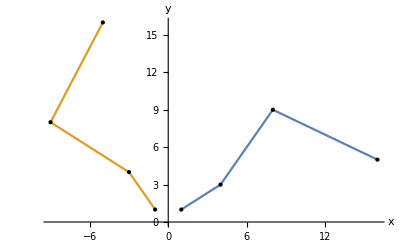

```mathematica
ListLinePlot[{e,eRotated},AxesLabel->{x,y},Epilog->{PointSize[Large],Point[e],Point[eRotated]}]
```

#### d)

I den sista deluppgiften använde vi ShearingTranform för att skjuva e 30 grader horisontellt. Med transformationsmatrisen A=(1 | 1/(√3) | 0
0 | 1 | 0
0 | 0 | 1) blev det möjligt att skjuva den.

```mathematica
eShear=ShearingTransform[30 Degree,{1,0},{0,1}]
```

TransformationFunction[(1 | 1/(√3) | 0
0 | 1 | 0
0 | 0 | 1)]

```mathematica
eShared=eShear[e]//N
```

{{1.57735,1.},{5.73205,3.},{13.1962,9.},{18.8868,5.}}

Nedan visas en model på den vanliga och den skjuvade e.

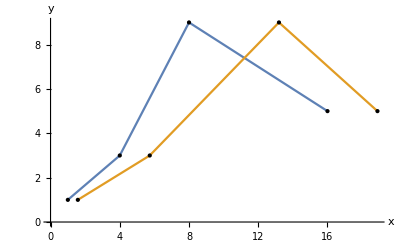

```mathematica
ListLinePlot[{e,eShared},AxesLabel->{x,y},Epilog->{PointSize[Large],Point[e],Point[eShared]}]
```

## 3. Resultat och slutsats

### 3.1 Uppgift 1 - Polynomanpassning

Med hjälp av reduced row echelon form fick vi de okända konstanterna (a,b,c,d,e) i fjärdegradspolynomet f(t) = a+ b t + c t^2+d t^3+e t^4.
 Vi fick att a = 1, b = -5 c = 4, d = 3 och e= -2. Vår slutliga funktion blev f(t) = 1-5 t+4 t^2+3 t^3-2 t^4 både med och utan Mathematica.
Nedan illustreras den plottade funktionen f(t) med hjälp av datatypen Plot.
-Graphics-

### 3.2 Uppgift 2 - Industriproduktion

Nedan är resultaten vi kom fram till efter att ha lagt upp evkationerna i mathematica.

p1 = 500, p2 = 300, p3 = 400.

### 3.3 Uppgift 3 - Linjärtransformationer och grafik

#### a)

Genom att använda tranfomationsmatrisen A=(2 | 0 | 0
0 | 2 | 0
0 | 0 | 1)  skalades matrisen från {{1,1},{4,3},{8,9},{16,5}} till {{2,2},{8,6},{16,18},{32,10}}, dvs storleken fördubblades.
Nedan illustreras de två matriser där den blåa är en den normala medan den oranga är den uppskalade matrisen. 
-Graphics-

#### b)

Transformationsmatrisen A=(-1 | 0 | 0
0 | 1 | 0
0 | 0 | 1) hjälpe oss att spegla (inversa x-kordinat)  matrisen e från {{1,1},{4,3},{8,9},{16,5}} till {{-1,1},{-4,3},{-8,9},{-16,5}}

Nedan kan man se att den inversa linjen är speglat mot den normala linjen.
-Graphics-

#### c)

90 graders rotation runt y axeln gjordes med transformationsmatrisen A=(0 | -1 | 0
1 | 0 | 0
0 | 0 | 1) på matrisen e där punkterna omvandlades {{-1,1},{-3,4},{-9,8},{-5,16}}.

Nedan visas slutresultatet av rotationen jämfört med den vanliga linjen.
-Graphics-

#### d)

I den sista deluppgiften använde vi A=(1 | 1/(√3) | 0
0 | 1 | 0
0 | 0 | 1) på matrisen e för att skjuva den 30 grader horisontellt. Matrisen omvandlades från {{1,1},{4,3},{8,9},{16,5}} till {{1.57735,1.},{5.73205,3.},{13.1962,9.},{18.8868,5.}}.

-Graphics-

Åvan kan vi se att den oranga linjen har skjuvat 30 grader från den blåa linjen.

### Slutsats

Under detta projekt har vi utvidgat våra kunskaper inom Mathematica. Detta genom att formulera diverse linjära ekvationssystem, ställa upp och åskådliggöra olika matrisoperationer. Vi har också lärt oss mycket mer om hur man går tillväga för att hitta funktioner med hjälp av reduced row echolon form.

Vi har även löst dessa uppgifter med hand, plottat funktioner och 2D punkter i mathematica samt att transformera dessa olika punkter med hjälp av olika funktioner inom mathematica. Projketet gav oss bra kunskap inom algerbraiska operationer och linjär algebra. Matte föreläsningar och övningar hjälpte oss mycket med att lösa alla uppgifter i projekt 1. Vi kommer forstätta att använda Mathematica till framtida matte projekter och för att lösa svåra matteuppgifter.